```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\neural-networks-tasks

```mathematica
Dimensions[Data=]
```

```mathematica
Data=Import["NG23T04Problem.xlsx",{"Sheets","Шпак Андрей"}]
```

```mathematica
Map[Dimensions,{Train,Test}=Partition[RandomSample@Data,UpTo[0.8*Length[Data]]]]
```

{{2400,3},{600,3}}

```mathematica
pts=Flatten[{Point[{#[[1]],#[[2]]}],If[#[[3]]==-1.,Red,Blue]}&/@Train]
```

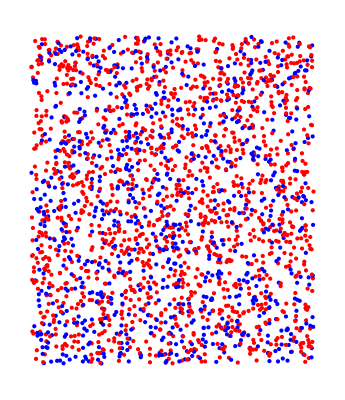

```mathematica
Graphics[{pts}]
```

# NG^23 T_04. Метод k-средних и RBF-сети

04-фев-2023
Шпак Андрей

## Section. Обучающий и тестирующий наборы

```mathematica
SetDirectory[NotebookDirectory[]]
Dimensions[Data=Import["NG23T04Problem.xlsx",{"Sheets","Шпак Андрей"}]]
```

D:\neural-networks-tasks

{3000,3}

```mathematica
Map[Dimensions,{Train,Test}=Partition[RandomSample@Data,UpTo[0.8*Length[Data]]]]
```

{{2400,3},{600,3}}

```mathematica
testList1[[All,3]]
```

{-1,1,-1}

```mathematica
Map[Dimensions,{TrainX=Train[[All,{1,2}]],TrainY=Rationalize@Train[[All,3]]}]
Map[Dimensions,{TestX=Train[[All,{1,2}]],TestY=Rationalize@Train[[All,3]]}]
```

{{2400,2},{2400}}

{{2400,2},{2400}}

```mathematica
Length[iBlue=Flatten@Position[TrainY,+1]]
Length[iRed=Flatten@Position[TrainY,-1]]
%%+%
```

882

1518

2400

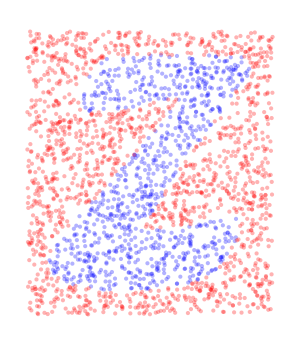

```mathematica
Fig0=Graphics[{PointSize@Medium,Opacity@.3,
Blue,Point@TrainX[[iBlue]],
Red,Point@TrainX[[iRed]]},
AspectRatio->Automatic,ImageSize->300]
```

## Section. Метод k-средних

```mathematica
test2={{98,62},{80,95},{71,130},{89,164},{137,115},{107,155},{109,105},{174,62},{183,115},{164,153},{142,174},{140,80},{308,123},{229,171},{195,237},{180,298},{179,340},{251,262},{300,176},{346,178},{311,237},{291,283},{254,340},{215,308},{239,223},{281,207},{283,156}}
```

{{98,62},{80,95},{71,130},{89,164},{137,115},{107,155},{109,105},{174,62},{183,115},{164,153},{142,174},{140,80},{308,123},{229,171},{195,237},{180,298},{179,340},{251,262},{300,176},{346,178},{311,237},{291,283},{254,340},{215,308},{239,223},{281,207},{283,156}}

```mathematica
n=2;
pts=RandomSample[test2,n];
clasters=Partition[pts,1]
```

{{{239,223}},{{251,262}}}

```mathematica
remainPts=Delete[test2,Flatten@Position[test2,pts[[#]]]&/@Range[1,n]]
```

{{98,62},{80,95},{71,130},{89,164},{137,115},{107,155},{109,105},{174,62},{183,115},{164,153},{142,174},{140,80},{308,123},{229,171},{195,237},{180,298},{179,340},{300,176},{346,178},{311,237},{291,283},{254,340},{215,308},{281,207},{283,156}}

```mathematica
While[Length@remainPts!=0,
For[i=1,i<=n,i++,
clasters[[i]]=Append[clasters[[i]],lstPt=Flatten@Nearest[remainPts,clasters[[i,-1]]]];
remainPts=Delete[remainPts,Flatten@Position[remainPts,lstPt]];
If[Length@remainPts==0,Break[],None];
]
]
```

```mathematica
clasters[[1]]
```

{{239,223},{281,207},{300,176},{283,156},{308,123},{183,115},{137,115},{109,105},{80,95},{71,130},{98,62},{195,237},{215,308},{254,340}}

```mathematica
clasters[[2]]
```

{{251,262},{291,283},{311,237},{346,178},{229,171},{164,153},{142,174},{107,155},{89,164},{140,80},{174,62},{180,298},{179,340}}

## Section. Логический оператор XOR и повышение размерности фазового пространства

## Section. Метод опорных векторов

### Section.Subsection. Исходное фазовое пространство

### Section.Subsection. Расширенное фазовое пространство

### Section.Subsection. Пошаговое выполнение алгоритма SVM

Рис 5. Построение разделительной полосы методом опорных векторов

### Section.Subsection. Разделительная полоса

## Section. Опорные точки

## Section. Множители Лагранжа и формулировка двойственной задачи

## Section. Последовательный метод активных ограничений

### Section.Subsection. Инициализация множества опорных точек

### Section.Subsection. Построение разделительной полосы

### Section.Subsection. Проверка опорных точек

### Section.Subsection. Ложная опорная точка

### Section.Subsection. Отступы

### Section.Subsection. Новая опорная точка

### Section.Subsection. Конец алгоритма